## Parametros del Modelo.

```mathematica
g:=2;
αs:=1/π;
αem := 1/137;
T=1.5/(.197);
eB=(.139)^2;
eq={2/3,1/3,1/3};
Δr=7/(.197);
R=7/(.197);
χ=.8;
λ=2;
μ=10^-15;
η=3;
β=0.25;
```

## Expresiones

```mathematica
n[ωp_,Λs_,m_,η_,β_]:=η/(Exp[(√(m^2+ ωp^2(1-β )^2/(1-β^2)))/Λs]-1);
```

```mathematica
V2[eB_,j_,Λs_,m_,η_,q_,β_]:=χ( 4/3 π T R^3)(αem*αs^2)/(2*(2π)^5)π eq[[j]]^2 NIntegrate[NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))( 2 ωp^2-ωp ωq+ ωq^2)(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])]-(1+(1-β )^2/(1-β^2)(ωp^2-ωp ωq+ωq^2)/(2 eB eq[[j]]))/((1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,ωq}],{ωq,0,q}];
(*Expresión para el V2, donde ya se hizo la integral sobre theta.*)
```

```mathematica
V2testOneInt[eB_,j_,Λs_,m_,η_,β_,ωq_,q_]:=χ( 4/3 π T R^3)(αem*αs^2)/(2*(2π)^5)π eq[[j]]^2 NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))( 2 ωp^2-ωp ωq+ ωq^2)(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,q}];
V2testOneInttwoterms[eB_,j_,Λs_,m_,η_,β_,ωq_,q_]:=χ( 4/3 π T R^3)(αem*αs^2)/(2*(2π)^5)π eq[[j]]^2 NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))( 2 ωp^2-ωp ωq+ ωq^2)(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])]-(1+(1-β )^2/(1-β^2)(ωp^2-ωp ωq+ωq^2)/(2 eB eq[[j]]))/((1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,q}];
```

## Pruebas v2

```mathematica
TestV2=Table[{q,V2testOneInt[1eB,1,λ,μ,η,β,0.5,q]+2V2testOneInt[1eB,2,λ,μ,η,β,0.5,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained 96.0803 and 0.544148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {5.04484×10^-9}. NIntegrate obtained 65.6467 and 0.187841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.17407×10^-9}. NIntegrate obtained 99.7296 and 0.270773 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.3,7.78004},{0.4,8.11973},{0.5,22.9335},{0.6,10.6202},{0.7,15.9207},{0.8,11.8686},{0.9,16.0144},{1.,9.47568},{1.1,16.1844},{1.2,10.7707},{1.3,16.3478},{1.4,13.3031},{1.5,10.6331},{1.6,11.7015},{1.7,15.7806},{1.8,20.931},{1.9,16.2515},{2.,9.5015},{2.1,10.2279},{2.2,32.0732},{2.3,15.6142},{2.4,10.4216},{2.5,9.67881},{2.6,15.9621},{2.7,15.7052},{2.8,11.6492},{2.9,9.36285},{3.,10.2191},{3.1,15.3447},{3.2,11.2707},{3.3,15.2905},{3.4,15.3444},{3.5,12.6806}}

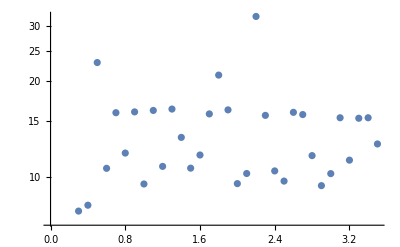

```mathematica
ListLogPlot[TestV2]
```

```mathematica
TestV2twoterms=Table[{q,V2testOneInttwoterms[1eB,1,λ,μ,η,β,0.5,q]+2V2testOneInttwoterms[1eB,2,λ,μ,η,β,0.5,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained -6.39175 and 0.0357583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained -2.60608 and 0.014495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.17407×10^-9}. NIntegrate obtained -6.66782 and 0.0177937 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.3,-0.464423},{0.4,-0.48468},{0.5,-1.3559},{0.6,-0.630884},{0.7,-0.924265},{0.8,-0.696929},{0.9,-0.936737},{1.,-0.678791},{1.1,-0.941492},{1.2,-0.622185},{1.3,-0.946982},{1.4,-0.880057},{1.5,-0.609009},{1.6,-0.670155},{1.7,-0.907971},{1.8,-1.20859},{1.9,-0.933482},{2.,-0.665006},{2.1,-0.578941},{2.2,-1.85793},{2.3,-0.893069},{2.4,-0.588293},{2.5,-0.544227},{2.6,-0.911774},{2.7,-0.896284},{2.8,-0.796266},{2.9,-0.523932},{3.,-0.573707},{3.1,-0.873654},{3.2,-0.634731},{3.3,-0.869895},{3.4,-0.872793},{3.5,-0.716505}}

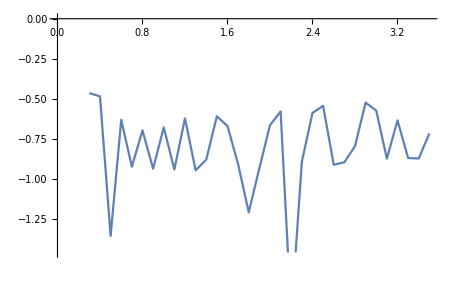

```mathematica
ListLinePlot[TestV2twoterms]
```

```mathematica
f=Interpolation[TestV2twoterms]
```

InterpolatingFunction[{{0.3, 3.5}}, <>]

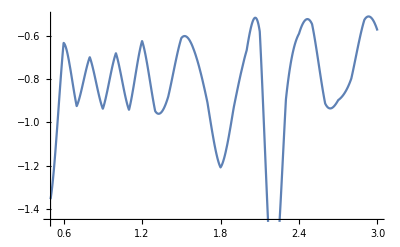

```mathematica
Plot[f[x],{x,0.5,3}]
```

```mathematica
Integrate[f[x],{x,0.5,3}]
```

-2.07996

```mathematica
TestV2=Table[{q,V2testOneInt[1eB,1,λ,μ,η,β,1.5,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained 74.6965 and 0.433428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.17407×10^-9}. NIntegrate obtained 75.2414 and 0.215665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {8.40807×10^-9}. NIntegrate obtained 78.4378 and 5.24795 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.3,4.50834},{0.4,4.54123},{0.5,4.73415},{0.6,4.65491},{0.7,5.06948},{0.8,4.72376},{0.9,4.7655},{1.,4.81874},{1.1,4.88688},{1.2,4.9807},{1.3,5.06717},{1.4,5.27201},{1.5,13.989},{1.6,12.9533},{1.7,11.9435},{1.8,6.24986},{1.9,10.3779},{2.,6.95316},{2.1,7.63817},{2.2,9.84051},{2.3,9.80233},{2.4,6.95196},{2.5,6.07211},{2.6,10.2647},{2.7,9.50728},{2.8,7.61205},{2.9,9.59331},{3.,5.50541},{3.1,6.19031},{3.2,6.952},{3.3,9.59067},{3.4,9.80629},{3.5,7.15196}}

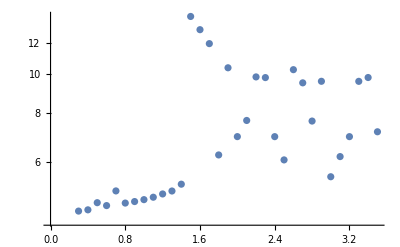

```mathematica
ListLogPlot[TestV2]
```

```mathematica
TestV2twoterms=Table[{q,V2testOneInttwoterms[1eB,1,λ,μ,η,β,1.5,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained -0.699815 and 0.00403602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.17407×10^-9}. NIntegrate obtained -0.706456 and 0.00200824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {4.36069×10^-11}. NIntegrate obtained -0.715966 and 0.00263855 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.3,-0.0422377},{0.4,-0.0426385},{0.5,-0.0432124},{0.6,-0.0439056},{0.7,-0.0441431},{0.8,-0.0447859},{0.9,-0.0453064},{1.,-0.0459417},{1.1,-0.0467227},{1.2,-0.0475732},{1.3,-0.0487101},{1.4,-0.0507767},{1.5,-0.132109},{1.6,-0.122308},{1.7,-0.112753},{1.8,-0.059593},{1.9,-0.0978975},{2.,-0.0658768},{2.1,-0.0721414},{2.2,-0.0925386},{2.3,-0.0920805},{2.4,-0.0654198},{2.5,-0.0571605},{2.6,-0.0961203},{2.7,-0.0889902},{2.8,-0.0712714},{2.9,-0.0896557},{3.,-0.0515292},{3.1,-0.0578503},{3.2,-0.064896},{3.3,-0.0894144},{3.4,-0.0913789},{3.5,-0.0769045}}

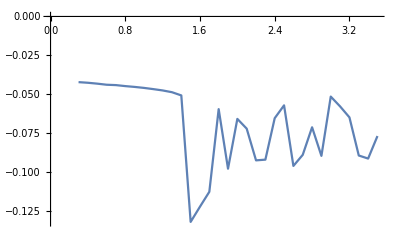

```mathematica
ListLinePlot[TestV2twoterms]
```

```mathematica
TestV2=Table[{q,V2testOneInt[1eB,1,λ,μ,η,β,3,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {5.04484×10^-9}. NIntegrate obtained 52.2054 and 0.153443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.17407×10^-9}. NIntegrate obtained 53.6812 and 0.154444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {4.36069×10^-11}. NIntegrate obtained 54.1858 and 0.202919 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.3,3.15088},{0.4,3.23995},{0.5,3.27041},{0.6,3.30772},{0.7,3.32459},{0.8,3.34454},{0.9,3.34762},{1.,3.36396},{1.1,3.38338},{1.2,3.39566},{1.3,3.40751},{1.4,3.4363},{1.5,3.44905},{1.6,3.4513},{1.7,3.46511},{1.8,3.4941},{1.9,3.51289},{2.,3.5323},{2.1,3.56437},{2.2,3.77216},{2.3,3.83024},{2.4,3.89229},{2.5,3.6443},{2.6,3.94189},{2.7,3.76341},{2.8,3.84534},{2.9,4.2091},{3.,10.7462},{3.1,9.97563},{3.2,9.30031},{3.3,6.81863},{3.4,8.54699},{3.5,5.68355}}

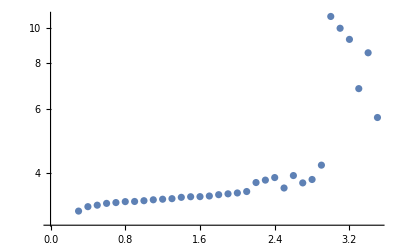

```mathematica
ListLogPlot[TestV2]
```

```mathematica
TestV2twoterms=Table[{q,V2testOneInttwoterms[1eB,1,λ,μ,η,β,3,q]},{q,.3,3.5,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {2.61642×10^-11}. NIntegrate obtained -0.126918 and 0.000735955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {7.57351×10^-16}. NIntegrate obtained -0.128126 and 0.000283467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {4.36069×10^-11}. NIntegrate obtained -0.129133 and 0.000481132 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.3,-0.00766018},{0.4,-0.00773308},{0.5,-0.00779389},{0.6,-0.00789092},{0.7,-0.00789845},{0.8,-0.00797189},{0.9,-0.00801285},{1.,-0.00806131},{1.1,-0.00811744},{1.2,-0.008157},{1.3,-0.00819593},{1.4,-0.00827541},{1.5,-0.00831724},{1.6,-0.00833458},{1.7,-0.00837971},{1.8,-0.00846119},{1.9,-0.00851887},{2.,-0.00857836},{2.1,-0.00866816},{2.2,-0.00872988},{2.3,-0.00878815},{2.4,-0.00880532},{2.5,-0.00891523},{2.6,-0.0090324},{2.7,-0.00919104},{2.8,-0.00939096},{2.9,-0.00969581},{3.,-0.0243978},{3.1,-0.0177993},{3.2,-0.0223766},{3.3,-0.0164743},{3.4,-0.0205596},{3.5,-0.0175361}}

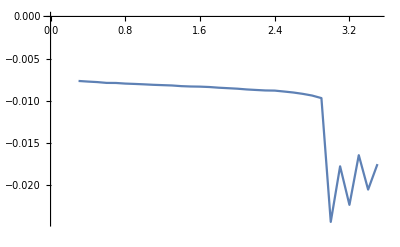

```mathematica
ListLinePlot[TestV2twoterms]
```

## Construyendo v2 (Jorge)

```mathematica
ListV21eB=Table[{ωq,V2[1eB,1,λ,μ,η,ωq,β]+2V2[1eB,2,λ,μ,η,ωq,β]},{ωq,.3,3.5,.1}]
```

NIntegrate::nlim: ωp = ωq is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωq near {ωq} = {0.031636}. NIntegrate obtained 15.7379 and 0.0034434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

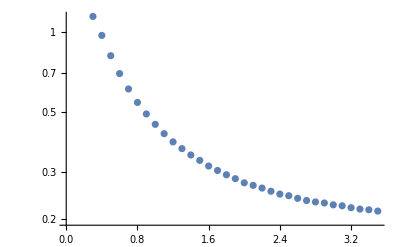

```mathematica
ListLogPlot[ListV21eB]
```